## Normal distribution

## Implementation of an automated process for generating normal distributions, and exporting them as graphical representations.

```mathematica
ClearAll["Global*`"]
```

### Generate the normal distribution

```mathematica
fNormal[x_,xargs_]:=1/xargs[[1]]*1/(√(2π))Exp[-1/2*((x-xargs[[2]])/xargs[[1]])^2];
normalData[xargs_,xmin_,xmax_]:=Table[{x,fNormal[x,xargs]},{x,xmin,xmax,(xmax-xmin)/100}];
```

### Helper functions for exporting graphics

```mathematica
pdfimage[name_,idx_]:=StringTemplate["``_``.pdf"][name,idx];
export[path_,object_]:=Export[StringTemplate["````"][NotebookDirectory[],path],object];
batchExport[objectname_,objectList_]:=Do[export[pdfimage[objectname,i],objectList[[i]]],{i,1,Length[objectList],1}];
```

### Create tester for exporting g_fx objects

```mathematica
rCircle[]:=Graphics[{Thickness[0.01],RandomColor[],Circle[]}];
batchExport["circleGfx",Table[rCircle[],{i,3}]]
```

## Calculation for the Area Under Curve

```mathematica
auc[xargs_,left_,right_]:=Integrate[fNormal[x,xargs],{x,left,right}];
aucN[xargs_,left_,right_]:=NIntegrate[fNormal[x,xargs],{x,left,right}];
```

## Implementation of the plotting function

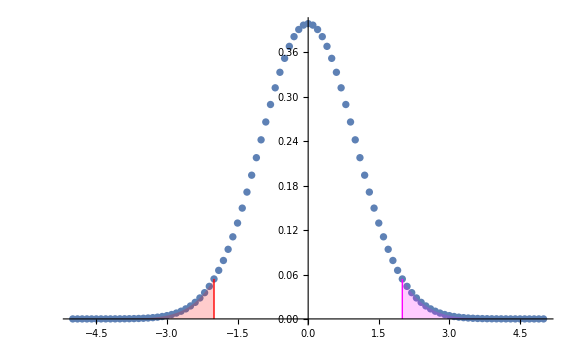

```mathematica
lines[xargs_,left_,right_]:=Graphics[{{Thick,Red,Line[{{left,0},{left,fNormal[left,xargs]}}]},{Thick,Magenta,Line[{{right,0},{right,fNormal[right,xargs]}}]}}];
leftTail[xargs_,xleft_,left_]:=Plot[fNormal[x,xargs],{x,xleft,left},PlotStyle->None,Filling->0,FillingStyle->Opacity[0.2,Red],PlotRange->Full];
rightTail[xargs_,xright_,right_]:=Plot[fNormal[x,xargs],{x,right,xright},PlotStyle->None,Filling->0,FillingStyle->Opacity[0.2,Magenta],PlotRange->Full];
plotter[data_,left_,right_]:=ListPlot[data,ImageSize->Large]
Show[plotter[normalData[{1,0},-5,5],-2,2],lines[{1,0},-2,2],leftTail[{1,0},-5,-2],rightTail[{1,0},2,5]]
```